## Calibration Curve to go from relative resistance to temperature.

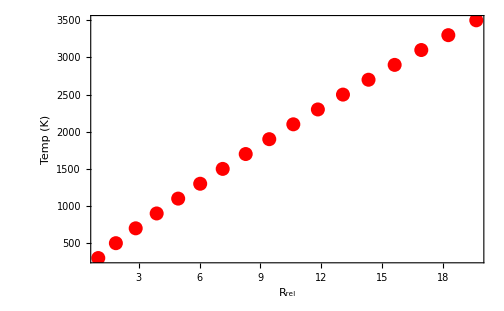

```mathematica
(* Data from manual. *)
TcalTemp={300,500,700,900,1100,1300,1500,1700,1900,2100,2300,2500,2700,2900,3100,3300,3500};
TcalRes={5.65,10.56,16.09,21.94,27.94,34.08,40.36,46.78,53.35,60.06,66.91,73.91,81.04,88.33,95.76,103.3,111.1};
TcalRrel=Table[TcalRes[[i]]/5.65,{i,1,Length[TcalRes]}];
Tcal=Table[{TcalRrel[[i]],TcalTemp[[i]]},{i,1,Length[TcalRrel]}];
p1=ListPlot[Tcal,PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},
Frame->True,FrameLabel->{"R_rel","Temp (K)","Stefan-Boltzmann Temperature Calibration"},
BaseStyle->FontSize->14,
ImageSize->7*72
]
```

## Fits to the calibration data.

Use TcalFit2. It gives an acceptable fit with a limited number of parameters in the fit.

```mathematica
TcalFit1=LinearModelFit[Tcal,x,x]
TcalFit1["BestFitParameters"]
TcalFit1["EstimatedVariance"]
TcalFit1["AdjustedRSquared"]
```

FittedModel[238.828+170.254 x]

{238.828,170.254}

2783.4

0.997271

```mathematica
TcalFit2=LinearModelFit[Tcal,{x,x^2},x]
TcalFit2["BestFitParameters"]
TcalFit2["EstimatedVariance"]
TcalFit2["AdjustedRSquared"]
```

FittedModel[122.375+204.163 x-1.67192 x^2]

{122.375,204.163,-1.67192}

89.51

0.999912

```mathematica
TcalFit3=LinearModelFit[Tcal,{x,x^2,x^3},x]
TcalFit3["BestFitParameters"]
TcalFit3["EstimatedVariance"]
TcalFit3["AdjustedRSquared"]
```

FittedModel[98.517+216.98 x-3.21169 x^2+0.0501034 x^3]

{98.517,216.98,-3.21169,0.0501034}

28.3918

0.999972

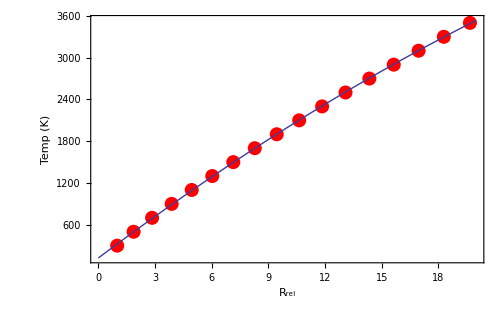

```mathematica
(* Use TcalFit2. *)
cal1=Plot[TcalFit2[x],{x,0,20}];
Show[p1,cal1]
```

## Now for the production data.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.87561×10^-12 | 5.1634×10^-13 | 3.6325 | 0.00546431
b | 3.99276 | 0.0371915 | 107.357 | 2.67929×10^-15
offset | 49.0828 | 0.000100872 | 486587. | 3.32988×10^-48

{a→1.87561×10^-12,b→3.99276,offset→49.0828}

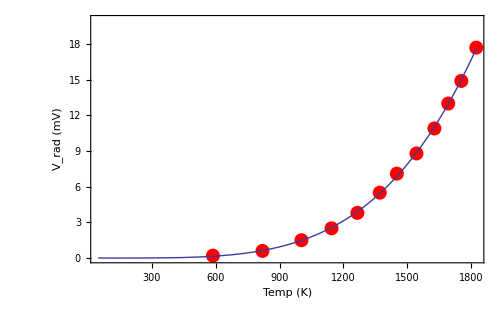

```mathematica
(* Resistance of bulb at room temp. *)
Rref=0.5; (* ohms.  *)
(* Measurements from power supply on the bulb in volts and amps. *)
Vs={0.987,1.9,3.0,4.0,5.0,6.1,7.0,8.0,9.1,10.1,11.0,12.1};
Is={0.85,1.08,1.34,1.53,1.70,1.89,2.03,2.16,2.31,2.45,2.56,2.69};
(* Voltage from rad sensor for production measurement. *)
Vrad={0.2,0.6,1.5,2.5,3.8,5.5,7.1,8.8,10.9,13.0,14.9,17.7};
(* Voltage from rad sensor with light shield in place. *)
Vb={0,0,0,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.4};
(* calculation of Rrel for each setting. *)
Rs=Table[Vs[[i]]/Is[[i]],{i,1,Length[Vs]}];
Rrel=Table[Rs[[i]]/Rref,{i,1,Length[Rs]}];
(* TableForm[Rrel] *)
TRad=Table[{TcalFit2[Rrel[[i]]],Vrad[[i]]},{i,1,Length[Vrad]}];
(* fit the results. *)
(* offset=330; *)
Clear[offset];
TRadFit=NonlinearModelFit[TRad, a*(x-offset)^b,{a,{b,4},offset},x];
TRadFit["BestFitParameters"];
TRadFit["ParameterTable"]
fit2=Plot[TRadFit[x],{x,0,TRad[[Length[TRad],1]]}];
fitResults1=TRadFit["BestFitParameters"]
exp=b/.fitResults1[[2]];
fitResults2=TRadFit["ParameterErrors"];
(* plot data and fit. *)
p2=ListPlot[TRad,PlotRange->{0,20},PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},
Frame->True,FrameLabel->{"Temp (K)","V_rad (mV)",
StringForm["n=`` ± ``, ES=``",NumberForm[exp,3],NumberForm[fitResults2[[2]],1],
NumberForm[TRadFit["EstimatedVariance"],3]]},
BaseStyle->FontSize->14,ImageSize->7*72
];
Show[p2,fit2]
```

```mathematica
Rs[[2]]
Rrel[[2]]
TcalFit2[Rrel[[2]]]
```

1.75926

3.51852

820.029

When I change Rrel from 0, 5 -> 0.4, I get the following errors. The fit is very fragile. See below for a more stable method.

NonlinearModelFit::nrlnum: The function value {-0.19427 - 0.00504097\ ⅈ, -0.6 + 0.\ ⅈ, -1.49459 + 0.\ ⅈ, -2.45936 + 0.\ ⅈ, -3.67239 + 0.\ ⅈ, -5.22476 + 0.\ ⅈ, -6.64817 + 0.\ ⅈ, -8.05724 + 0.\ ⅈ, -9.78927 + 0.\ ⅈ, -11.5266 + 0.\ ⅈ, -13.0105 + 0.\ ⅈ, -15.2357 + 0.\ ⅈ} is not a list of real numbers with dimensions {12} at {a, b, offset} = {5.37821×10^-12, 3.77034, 968.486}.

FittedModel::varnum: The estimated variance 87.6304  + 0.000217624\ ⅈ
 is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Missing[]

FittedModel::varnum: The estimated variance 87.6304  + 0.000217624\ ⅈ
 is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Part::partw: Part 2 of Missing[] does not exist.

FittedModel::varnum: The estimated variance 87.6304  + 0.000217624\ ⅈ
 is not a positive number. Properties requiring division by the variance or standard error will not be computed.

## An attempt at a more stable fitting procedure.

This seems to work. I can change Rref over the range 0.2-1.0 and I still get reasonable fit. If I change Rref too much, then the slope does not agree as well with the expected value of 4.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11.9426 | 0.168567 | -70.8476 | 7.65394×10^-15
x | 4.0415 | 0.054208 | 74.5554 | 4.59973×10^-15

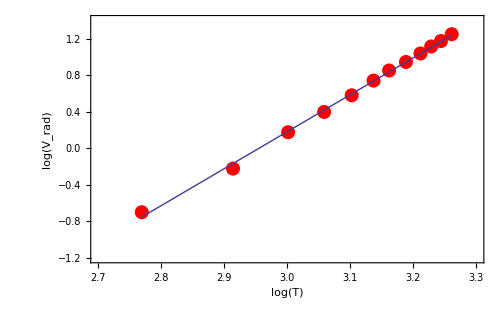

```mathematica
(* Start with the same stuff as before: resistance of bulb at room temp. *)
Rref=0.5; (* ohms.  *)
(* Measurements from power supply on the bulb in volts and amps. *)
Vs={0.987,1.9,3.0,4.0,5.0,6.1,7.0,8.0,9.1,10.1,11.0,12.1};
Is={0.85,1.08,1.34,1.53,1.70,1.89,2.03,2.16,2.31,2.45,2.56,2.69};
(* Voltage from rad sensor for production measurement. *)
Vrad={0.2,0.6,1.5,2.5,3.8,5.5,7.1,8.8,10.9,13.0,14.9,17.7};
(* Voltage from rad sensor with light shield in place. *)
Vb={0,0,0,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.4};
(* calculation of Rrel for each setting. *)
Rs=Table[Vs[[i]]/Is[[i]],{i,1,Length[Vs]}];
Rrel=Table[Rs[[i]]/Rref,{i,1,Length[Rs]}];
(* TableForm[Rrel] *)
TRad=Table[{TcalFit2[Rrel[[i]]],Vrad[[i]]},{i,1,Length[Vrad]}];
(* now do the fitting differently using logs. *)
TRad2=Table[{Log[10,TcalFit2[Rrel[[i]]]],Log[10,Vrad[[i]]]},{i,1,Length[Vrad]}];
TRadFit2=LinearModelFit[TRad2,{x},x];
TRadFit2["BestFitParameters"];
TRadFit2["ParameterTable"]
fit3=Plot[TRadFit2[x],{x,Log[10,TRad[[1,1]]],Log[10,TRad[[Length[TRad],1]]]}];
fitResults3=TRadFit2["BestFitParameters"];
fitResults4=TRadFit2["ParameterErrors"];
(* plot data and fit. *)
p3=ListPlot[TRad2,PlotRange->{{2.7,3.3},{-1.2,1.4}},PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},
Frame->True,FrameLabel->{"log(T)","log(V_rad)",
StringForm["n=`` ± ``, ES=``",NumberForm[fitResults3[[2]],3],NumberForm[fitResults4[[2]],1],
NumberForm[TRadFit2["EstimatedVariance"],3]]},
BaseStyle->FontSize->14,ImageSize->7*72
];
Show[p3,fit3]
```

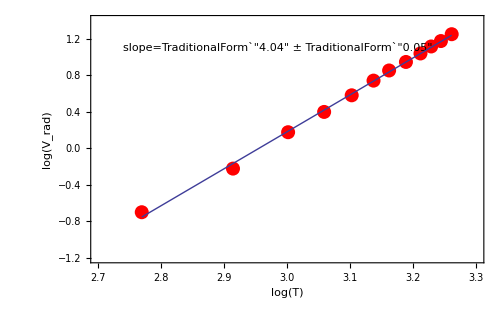

```mathematica
p4=ListPlot[TRad2,PlotRange->{{2.7,3.3},{-1.2,1.4}},PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},
Frame->True,FrameLabel->{"log(T)","log(V_rad)","Stefan-Boltzmann Law"},
BaseStyle->FontSize->14,ImageSize->7*72
];
p5=Show[p4,fit3,
Graphics[Text[StringForm["slope=`` ± ``",NumberForm[fitResults3[[2]],3],NumberForm[fitResults4[[2]],1]],{2.74,1.1},{-1,0}]]]
```

```mathematica
Export["/media/ADATA UFD/iqs/stefanBoltzmann/stefansLaw1.png",p5]
```

/media/ADATA UFD/iqs/stefanBoltzmann/stefansLaw1.png

{0.0526987,-0.0554839,-0.0110933,-0.0203671,-0.0153801,0.00515703,0.0161344,0.00135588,0.00104892,0.00894251,0.00561978,0.0113672}

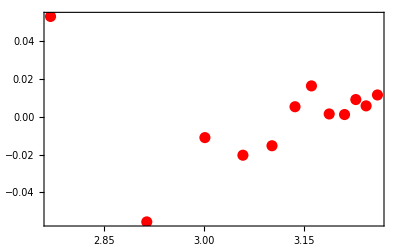

```mathematica
t11=TRadFit2["FitResiduals"]
t10 = Table[{TRad2[[i,1]],t11[[i]]},{i,1,Length[t11]}];
ListPlot[t10,PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},Frame->True]
```